#### EE[] function is the dispersion relationship, kx, ky are moments and a, b are lattice constants. for Square lattice a=b.

```mathematica
EE[a_,b_,kx_,ky_]:=-2(Cos[kx a]+Cos[ky b]);
```

#### Band-structure when a=b=1 with 3D, 2D color plot, and 2D contour plot.

```mathematica
Plot3D[EE[1,1,x,y],{x,-Pi/1,Pi/1},{y,-Pi/1,Pi/1},AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

```mathematica
MatrixPlot[Table[-2Cos[m Pi/100]-2Cos[n Pi/100],{m,-100,100},{n,-100,100}],
ColorFunction->"TemperatureMap",PlotLegends->Automatic,Epilog->{Red,Text[Style[Γ,16],{100,100}],Blue,Text[Style[M,16],{195,195}],Black,Text[Style[X,16],{195,100}]}]
```

-Graphics-

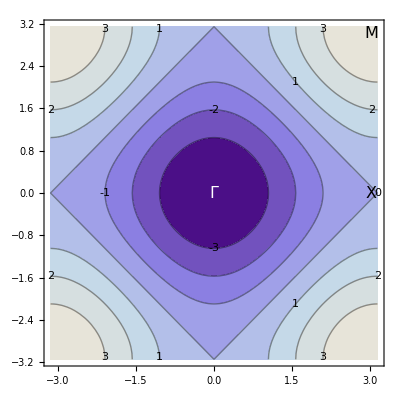

```mathematica
ContourPlot[EE[1,1,x,y],{x,-Pi/1,Pi/1},{y,-Pi/1,Pi/1},Epilog->{White,Text[Style[Γ,16],{0,0}],Black,Text[Style[M,16],{Pi-0.12,Pi-0.12}],Black,Text[Style[X,16],{Pi-0.12,0}]},ContourLabels->All]
```

#### Band-structure along closed path in brilluoin zone which connecting high symmetry points Γ, M, X.

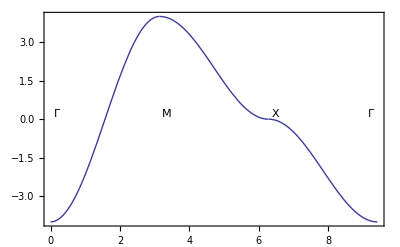

```mathematica
F[A_,B_]:=EE[1,1,A,B]
Plot[Piecewise[{{F[t,t],t≥0&&t<Pi},{F[Pi,-t+2Pi],t≥Pi&&t<2Pi},{F[Pi-t+2Pi,0],t≥2Pi&&t≤3Pi}}],{t,0,3Pi},Frame->True,GridLines->{{{Pi,Dashed},{2Pi,Dashed},{0,Dashed},{3Pi,Dashed}},{}},Epilog->{Inset["Γ",{0.2,0.2}],Inset["M",{Pi+0.2,0.2}],Inset["X",{2Pi+0.2,0.2}],Inset["Γ",{3Pi-0.2,0.2}]}]
```

## The density of state, use Lorenz form of Dirac delta function.

```mathematica
DRAC[t_,δ_]:=δ/Pi/(t^2+δ^2);
```

```mathematica
Dos[e_]:=NIntegrate[DRAC[e-EE[1,1,x,y],0.1],{x,-Pi,Pi},{y,-Pi,Pi}];
```

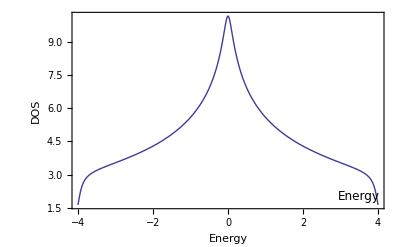

```mathematica
Plot[Dos[z],{z,-4,4},PlotRange->Full,Frame->True,AxesLabel->{Energy,DOS},Epilog->{Inset[Style["Energy",12],{3.5,2}]}]
```

#### The spectral density function

```mathematica
A[kx_,ky_,ϵ_,δ_]:=δ/Pi/((ϵ-EE[1,1,kx,ky])^2+δ^2)
```

```mathematica
Plot3D[Piecewise[{{A[t,t,e,0.5],t≥0&&t≤Pi},{A[Pi,-t+2Pi,e,0.5],t≥Pi&&t≤2Pi},{A[Pi-t+2Pi,0,e,0.5],t≥2Pi&&t≤3Pi}}],{t,0,3Pi},{e,-4,4}]
```

-Graphics3D-

```mathematica
DensityPlot[Piecewise[{{A[t,t,e,0.5],t≥0&&t≤Pi},{A[Pi,-t+2Pi,e,0.5],t≥Pi&&t≤2Pi},{A[Pi-t+2Pi,0,e,0.5],t≥2Pi&&t≤3Pi}}],{t,0,3Pi},{e,-4,4},ColorFunction->"SunsetColors",PlotLegends->Automatic]
```

-Graphics-

#### MDC, kx=ky={π/6,π/6+0.3,π/6+0.6,π/6+0.9,π/6+1.2,}

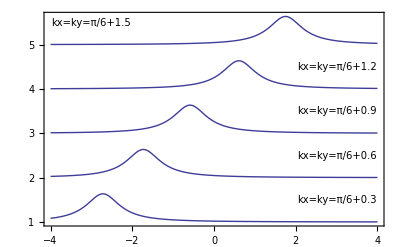

```mathematica
Plot[Table[A[Pi/6+0.3 i,Pi/6+0.3i,e,0.5]+i,{i,5}],{e,-4,4},PlotRange->Full,Epilog->{Inset[Style["kx=ky=π/6+0.3",10],{3,1.5}],Inset[Style["kx=ky=π/6+0.6",10],{3,2.5}],Inset[Style["kx=ky=π/6+0.9",10],{3,3.5}],Inset[Style["kx=ky=π/6+1.2",10],{3,4.5}],Inset[Style["kx=ky=π/6+1.5",10],{-3,5.5}]},Frame->True]
```

#### EDC, E={-2,-1,0,1,2}

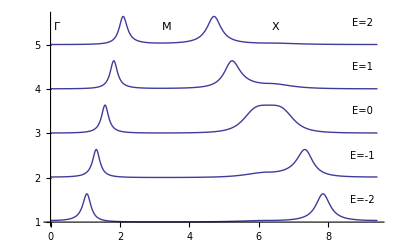

```mathematica
Plot[Table[Piecewise[{{A[t,t,e-3,0.5],t≥0&&t≤Pi},{A[Pi,-t+2Pi,e-3,0.5],t≥Pi&&t≤2Pi},{A[Pi-t+2Pi,0,e-3,0.5],t≥2Pi&&t≤3Pi}}]+e,{e,5}],{t,0,3Pi},PlotRange->Full,Epilog->{Inset[Style["E=-2",10],{9,1.5}],Inset[Style["E=-1",10],{9,2.5}],Inset[Style["E=0",10],{9,3.5}],Inset[Style["E=1",10],{9,4.5}],Inset[Style["E=2",10],{9,5.5}],Inset["Γ",{0.2,5.4}],Inset["M",{Pi+0.2,5.4}],Inset["X",{2Pi+0.2,5.4}]},GridLines->{{{Pi,Dashed},{2Pi,Dashed},{0,Dashed},{3Pi,Dashed}},{}}]
```

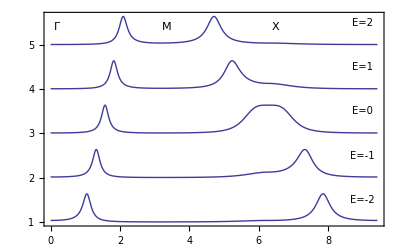

```mathematica
Show[%351,Frame->True]
```

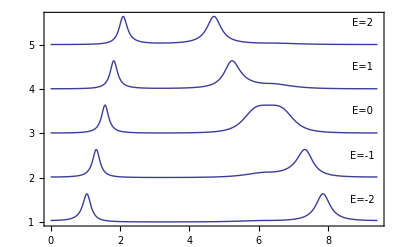

```mathematica
Show[%251,Frame->True]
```

```mathematica
Array[Eee,200];
```

```mathematica
nn=1;While[nn<201,Eee[nn]=0;nn++]
```

```mathematica
(*-------- Improved by YLL --------*)
For[i=0,i≤200,i++,
For[j=0,j≤200,j++,
{
energy=EE[1,1,i Pi/100-Pi,j Pi/100-Pi]//N;    (* make sure energy is represented in the form 1.234 and not Cos[...] *)
n=Rescale[energy,{-4.1,4.1},{1,200}]//Round;    (* find appropriate bin *)
Eee[n]++
}
]
]
```

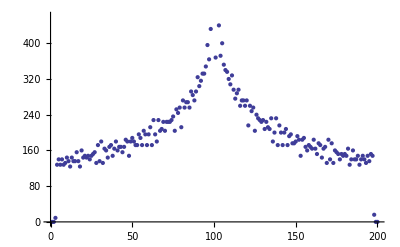

```mathematica
ListPlot[Table[{i,Eee[i]},{i,1,200}]]
```

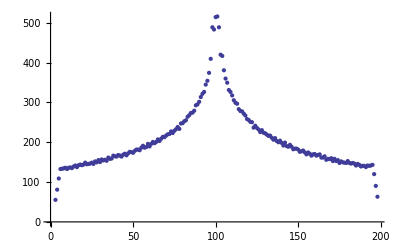

```mathematica
ListPlot[Table[{i,(Eee[i]+Eee[i+1]+Eee[i+2]+Eee[i-1]+Eee[i-2])/5},{i,3,198}]]
```